# “Simple model of self-supported deformed states of isolated atoms”

### Obliczenia analityczne

1) zakładamy nieskończenie ciężkie jądro atomowe: m_n ⟶ ∞, pomijamy człon p⃗ P⃗ w równianiu (6)
2) przyjęte współrzędne na płaszczyźnie (X,Y): r⃗=(r
0), p⃗=(0
p), R⃗=(R
0), P⃗=(0
P)
3) prędkość kątowa ω w kierunku Z, więc: ω⃗ x r⃗=(0
ωr
0), ω⃗ x p⃗=(-ωp
0
0), ω⃗ x R⃗=(0
ωR
0), ω⃗ x P⃗=(-ωP
0
0)
4) równania (7) na warunki stabilności układu - przyrównujemy pochodne po czasie do zera:

Piecewise[{{p/m_e=ωr, (a)}, {P/m_c=ωR
0 = -Z/r^2+(Z-1)/(R-r)^2+ωp
0 = -kR-(Z-1)/(R-r)^2+ωP, (b)

(c)

(d)}}]

### Parametry symulacji

```mathematica
me=1; (* masa elektronu rydbergowskiego*)
mc=(Z-1); (* masa chmury elektronowej *)
k=3.5; (* stała sprężystości oscylatora *)
Z=12; (* liczba atomowa, atom magnezu Mg*)
```

### Warunki stabilności układu

```mathematica
eqs={p/me==w r, pp/mc==w rr, 0==-Z/r^2+(Z-1)/(rr-r)^2+w p, 0==-k rr - (Z-1)/(rr-r)^2+w pp} (* stabilne położenia i pędy w funkcji ω *)
```

{p==r w,pp/11==rr w,0==-12/r^2+11/(-r+rr)^2+p w,0==-3.5 rr-11/(-r+rr)^2+pp w}

```mathematica
(*Plot[{r,-rr}/.(rozw=NSolve[eqs/.w-> ww,{p,pp,r,rr},Reals];rozw[[Flatten[Position[Negative[rozw[[#1,3,2]] rozw[[#1,4,2]]&@Table[i,{i,3}]],True]][[1]]]]),{ww,0.01,0.55},ImageSize->Large,AxesLabel->{"ω","{r,-R}"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}] (* rozwiązanie układu równań i rysowanie "fizycznych" (rR<0) rozwiązań {r,-R} w funkcji częstości kołowej ω *)*)
```

### LFT (31.10.2015)

```mathematica
me=1; (* masa elektronu rydbergowskiego*)
mc=(Z-1); (* masa chmury elektronowej *)
k=3.5; (* stała sprężystości oscylatora *)
Z=12; (* liczba atomowa, atom magnezu Mg*)
ww=0.1;
```

```mathematica
h=(px1^2+py1^2)/2+(pxx1^2+pyy1^2)/(2 mc)+k(xx1^2+yy1^2)/2-Z/Sqrt[x1^2+y1^2]+(Z-1)/Sqrt[(x1-xx1)^2+(y1-yy1)^2]-ww(x1 py1 - y1 px1 + xx1 pyy1 - yy1 pxx1)
```

1/2 (px1^2+py1^2)+1/22 (pxx1^2+pyy1^2)-12/(√(x1^2+y1^2))+11/(√((x1-xx1)^2+(y1-yy1)^2))-0.1 (py1 x1+pyy1 xx1-px1 y1-pxx1 yy1)+1.75 (xx1^2+yy1^2)

```mathematica
row1={xdot1==D[h,px1],
ydot1==D[h,py1],
xxdot1==D[h,pxx1],
yydot1==D[h,pyy1],
pxdot1==-D[h,x1],
pxxdot1==-D[h,xx1],
pydot1==-D[h,y1],
pyydot1==-D[h,yy1]}
```

{xdot1==px1+0.1 y1,ydot1==py1-0.1 x1,xxdot1==pxx1/11+0.1 yy1,yydot1==pyy1/11-0.1 xx1,pxdot1==0.1 py1-(12 x1)/((x1^2+y1^2)^(3/2))+(11 (x1-xx1))/(((x1-xx1)^2+(y1-yy1)^2)^(3/2)),pxxdot1==0.1 pyy1-3.5 xx1-(11 (x1-xx1))/(((x1-xx1)^2+(y1-yy1)^2)^(3/2)),pydot1==-0.1 px1-(12 y1)/((x1^2+y1^2)^(3/2))+(11 (y1-yy1))/(((x1-xx1)^2+(y1-yy1)^2)^(3/2)),pyydot1==-0.1 pxx1-(11 (y1-yy1))/(((x1-xx1)^2+(y1-yy1)^2)^(3/2))-3.5 yy1}

```mathematica
pod={x1->x[t],xdot1->x'[t],y1->y[t],ydot1->y'[t],xx1->xx[t],xxdot1->xx'[t],yy1->yy[t],yydot1->yy'[t],px1->px[t],pxdot1->px'[t],py1->py[t],pydot1->py'[t],pxx1->pxx[t],pxxdot1->pxx'[t],pyy1->pyy[t],pyydot1->pyy'[t]}
```

{x1→x[t],xdot1→x'[t],y1→y[t],ydot1→y'[t],xx1→xx[t],xxdot1→xx'[t],yy1→yy[t],yydot1→yy'[t],px1→px[t],pxdot1→px'[t],py1→py[t],pydot1→py'[t],pxx1→pxx[t],pxxdot1→pxx'[t],pyy1→pyy[t],pyydot1→pyy'[t]}

```mathematica
row=row1/.pod
```

{x'[t]==px[t]+0.1 y[t],y'[t]==py[t]-0.1 x[t],xx'[t]==pxx[t]/11+0.1 yy[t],yy'[t]==pyy[t]/11-0.1 xx[t],px'[t]==0.1 py[t]-(12 x[t])/((x[t]^2+y[t]^2)^(3/2))+(11 (x[t]-xx[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2)),pxx'[t]==0.1 pyy[t]-3.5 xx[t]-(11 (x[t]-xx[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2)),py'[t]==-0.1 px[t]-(12 y[t])/((x[t]^2+y[t]^2)^(3/2))+(11 (y[t]-yy[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2)),pyy'[t]==-0.1 pxx[t]-(11 (y[t]-yy[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2))-3.5 yy[t]}

```mathematica
warpoc={x[0]==xrown,y[0]==0,xx[0]==xxrown,yy[0]==0,px[0]==0,py[0]==pyrown,pxx[0]==0,pyy[0]==pyyrown}
```

{x[0]==xrown,y[0]==0,xx[0]==xxrown,yy[0]==0,px[0]==0,py[0]==pyrown,pxx[0]==0,pyy[0]==pyyrown}

```mathematica
eqs={p/me==w r, pp/mc==w rr, 0==-Z/r^2+(Z-1)/(rr-r)^2+w p, 0==-k rr - (Z-1)/(rr-r)^2+w pp}
```

{p==r w,pp/11==rr w,0==-12/r^2+11/(-r+rr)^2+p w,0==-3.5 rr-11/(-r+rr)^2+pp w}

```mathematica
rozw=NSolve[eqs/.w-> ww,{p,pp,r,rr},Reals];
rozw1=rozw[[Flatten[Position[Negative[rozw[[#1,3,2]] rozw[[#1,4,2]]&@Table[i,{i,3}]],True]][[1]]]]
```

{p→0.526022,pp→-0.123655,rr→-0.112414,r→5.26022}

```mathematica
warpoc=warpoc/.{xrown->rozw1[[4,2]],xxrown->rozw1[[3,2]],pyrown->rozw1[[1,2]],pyyrown->rozw1[[2,2]]}
```

{x[0]==5.26022,y[0]==0,xx[0]==-0.112414,yy[0]==0,px[0]==0,py[0]==0.526022,pxx[0]==0,pyy[0]==-0.123655}

```mathematica
rownania=Flatten[{row,warpoc},1]
```

{x'[t]==px[t]+0.1 y[t],y'[t]==py[t]-0.1 x[t],xx'[t]==pxx[t]/11+0.1 yy[t],yy'[t]==pyy[t]/11-0.1 xx[t],px'[t]==0.1 py[t]-(12 x[t])/((x[t]^2+y[t]^2)^(3/2))+(11 (x[t]-xx[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2)),pxx'[t]==0.1 pyy[t]-3.5 xx[t]-(11 (x[t]-xx[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2)),py'[t]==-0.1 px[t]-(12 y[t])/((x[t]^2+y[t]^2)^(3/2))+(11 (y[t]-yy[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2)),pyy'[t]==-0.1 pxx[t]-(11 (y[t]-yy[t]))/(((x[t]-xx[t])^2+(y[t]-yy[t])^2)^(3/2))-3.5 yy[t],x[0]==5.26022,y[0]==0,xx[0]==-0.112414,yy[0]==0,px[0]==0,py[0]==0.526022,pxx[0]==0,pyy[0]==-0.123655}

```mathematica
tmax=1;
```

```mathematica
s=NDSolve[rownania,{x,xx,y,yy,px,pxx,py,pyy},{t,0,tmax}]
```

{{x→InterpolatingFunction[{{0., 1.}}, <>],xx→InterpolatingFunction[{{0., 1.}}, <>],y→InterpolatingFunction[{{0., 1.}}, <>],yy→InterpolatingFunction[{{0., 1.}}, <>],px→InterpolatingFunction[{{0., 1.}}, <>],pxx→InterpolatingFunction[{{0., 1.}}, <>],py→InterpolatingFunction[{{0., 1.}}, <>],pyy→InterpolatingFunction[{{0., 1.}}, <>]}}

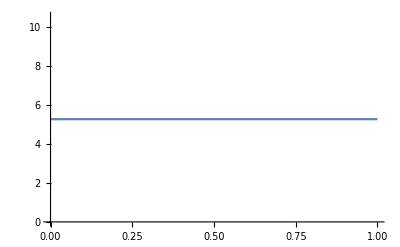

```mathematica
Plot[x[t]/.s,{t,0,tmax}]
```